# College IBM

## DG

```mathematica
Today[]
SetDirectory["C:\\College\\Coding\\Campus"]
```

Mon 18 Jul 2022[]

C:\College\Coding\Campus

```mathematica
"C:\\College\Coding\Campus
```

### Overview of college community

Specific features of a college community are structured social interactions, which combine scheduled and random contacts. The former include scheduled classes and residence (dorms), while all other (unscheduled) activities are lumped into random social contacts, described below. We make another departure from the previous case in our basic setup of disease states and progress history.  Instead of 4 convectional SEIR stages, we assume a graded infectivity which changes in time following a prescribed infectivity pattern described below.
Our college model features two basic components.  Part (i) allows to generate a synthetic college community from a few basic inputs (below). That will include their scheduled and random contacts. Part (ii) describes disease patterns and host (student) body makeup in terms of their susceptibility (immune status) , vaccination status, and progress pathways (Mild, Severe, Vaccinated). The two parts are used to setup the basic ‘dynamic step’. The model is run in discrete time steps (1 day). The state of the system is an association “host id” -> “host infective status”. The latter includes (S,I,R) - label augmented for I-stage its duration (day from the onset of infection), and disease pathway (L - light , H -heavy/severe, V - vaccinated). L-H-V pathways are inherent host traits, maintained in the course of infection. They determine host infectivity and duration of the I-stage (disease pattern) , as well as its symptomatic expression, hence test outcomes and quarantine isolation. 
An example of system (community) state: <|S_1 -{S,L},S_2→{{I,3},H},S_3→{R,V}...|> , meaning  host S_1 of ‘light pathway’ is susceptible,  S_2 (‘heavy pathway’) is on the 3rd day of infection, while S_3 (‘vaccinated pathway’) has recovered (immune). The dynamic code will update the system state to the next day based on their daily interactions and interventions. 
Contact pools arising in different settings (class, dorm, social) bring together susceptible and infective hosts, and thereby drive transmission. Class contacts are different from others, as they depend on class seating (assigned to each classroom). Having an infective host at a particular seat, the transmission probability drops with the distance, so only nearest neighbors share the highest risk. Other contact pools do not include spatial specifics, but each type of environment (classroom, dorm, social) carries a (mean) environmental risk factor {a_C,a_D,a_S}, that module survival probability function p_S.
The basic model inputs include (i) initial community state, (ii) class and dorm schedule and parameters of random social mixing, (iii) environmental risk factors. An extended version includes control interventions: symptomatic isolation, random screening, vaccination.

## Codes

### Mixing and disease progress

#### Social mixing

Patterns:
1) Partition of total host-pool (HP) into nonoverlapping random pools of sizes m <# <n
2) Pool-size distribution: 
size | m1 | ... | mk
frequency | f1 | ... | fk ; f1+f2+...+fk=1
Generate overlapping random pools of sizes {m1,m2,...} with per-host frequences {f1,f2,...}
Mean contact rate/day: f1*m1(m1-1)+f2*m2(m2-1)+...

```mathematica
(*Nonoverlapping partition of pool hp into mixing pools of sizes 
pos={m1, m2,...}, with weights= wei*)
RanMixN[hp_,{wei_,pos_}]:=
Block[{L=Length@hp,mm,pz},
(*random pools wth weights wei*)mm=RandomChoice[wei->pos,(*L/mean poool size*)Floor[(L Total@wei)/(wei.pos)]];
pz=TakeList[RandomSample@hp,UpTo/@mm];
Select[pz,Length[#]>1&]]
(*Random overlapping mixing clusters on weights= wei, sizes= pos, and mean intensity (frequancy) of social mixing/day = om*)
RanMixC[hp_,{wei_,pos_,om_:1}]:=
Block[{L=Length@hp,nP,mm},
(*# pools*)nP=Floor[om(L Total@wei)/(wei.pos)];
mm=RandomChoice[wei->pos,nP];
RandomSample[hp,#]&/@mm]
```

```mathematica
(*Complement map to generate mixing contacts for a pool L*)
CompFun[L_]:=#->Complement[L,{#}]&/@L
```

#### Disease progress/recovery for I-pool

Disease States: we assume 3 disease states S-I-R (susceptible, infected, or recovered). But unlike previous case (simple SEIR), the I-state is graded by the day past infection,  0<=d<=L (disease duration). In the course of infection, host undergoes different stages of disease marked by infectivity function b(d) that serves as a proxy for viral load, and measures the probability of transmission to a fully susceptible host. Typical viral load and the infectivity function, follows a U-shape pattern of Fig. 2, with steep initial growth phase followed by slower drop due to immune activation and parasite clearing.  Such graded infectivity (age of disease)  is widely used in infectious disease modeling (see e.g.  [15]), and our profiles (below) are qualitatively consistent with observed patterns [16].
Different analytic functional forms ϕ(x) can be used to reproduce such patterns. Here we use Gamma-type function ϕ(x)=x^p e^(-p (1-x)) of rescaled time variable x=d/P (P - peak parasitemia) which attains its maximum at x=1, and has steepness (shape-parameter) p . The infectivity is given by b(d)=B*ϕ(d/P), with maximal infectivity =B, and peak timing = P (3-7 days) [5, 6]. The effective duration of the resulting I-stage varies in the range: 2.5*P<L<4*P

3 progress pathways:  pw = “S”- symptomatic; “M” - mild,”V”- vaccinated

```mathematica
(*I-Progress*)ProG[{1,d_,pw_}]:=Piecewise[{{{1,d+1,pw}, d<=L[pw]}, {{2,pw}, True}}];
(*Quarantine progress*)ProG[{Q,d_,pw_}]:=Piecewise[{{{Q,d+1,pw}, d<=L[pw]}, {{2,pw}, True}}];
(*all other*)ProG[z_]:=z;
```

```mathematica
(*S-progress: state c={0,pw}+ Bernoulli value p=0 or p=1. If p=0 (no infection) or p -absent (no contact), c->c; if p=1 (infection S->I) c={0,pathawy}->{1, 0, Pathway}*)
SProgF[{c_,b_:0}]:=If[b==1,Prepend[c,1],c]
(*Bernoulli probability f-n for transitions: E->I->...->R, in terms of stage duration = x*)
ϕ[x_,m_]=x^m/(1+x^m);
(*Disease progress as f-n of probability of infection =a, for S-state*)
RanBernDraw[a_]:=RandomVariate[BernoulliDistribution@a]
SetAttributes[RanBernDraw,Listable]
```

#### Infectivity function

Disease Pathways. For Covid-19, infection patterns can differ markedly in terms of duration and severity, ranging from mild (asymptomatic) infection to long term severe disease and death [7]. The risk factors of disease are strongly associated with age and health status. In our college model made of young-age population, we allow three disease pathways: Mild (M), Severe (S), and Vaccinated (V). They differ in terms of maximal infectivity b_m , duration L; we fixed steepness parameter p=3.  Putative values are listed below [5, 6]

□ | Effective duration (L) | Max infectivity (b_m)
Mild | 12 | .2
Severe | 21 | .3
Vaccinated | 9 | .15
Table 1: Plausible choices for disease pathway parameters

Accordingly, host population is divided into 3 progress groups: (M), (S), (V) with prescribed fractions f_M+f_S+f_V=1. More generally, one could allow a broad range of in-host pathway parameters, so each host in the IBM community could follow its own history.

The basic infection step (S→I) is determined by random Bernoulli draw  of probability  p_I. The ‘S-progress function’ used in the main code (below) allows for different cases of S- state, c={0, pathway}, and Bernoulli value b = 0,1 or absent (no mixing contacts).

```mathematica
(*Basic infectivity profile*)
BiF[x_,p_]=x^p Exp[p(1-x)];
(*infectivity f-n*)
inF[Missing[__]]=0;
inF[{0,___}]=0;
inF[{2,___}]=0;
inF[{Q,___}]=0;
inF[{1,d_,pw_}]:=(*max infectivity*)maxI[pw](*temporal pattern*)BiF[3 d/L[pw],(*steepness*)3]
(*Max infectivity*)
{maxI["M"],maxI["S"],maxI["V"]}={.2,.25,.15};
(*I-stage durartion*){L["M"],L["S"],L["V"]}={12,21,9};
(*Disease pathway suscepitibility: assume "V"-hosts have 20% suceptibility of M-S*)
{aH["M"],aH["S"],aH["V"],aH[2]}={1,1,.5,0};
```

#### Probability of S-survival in class/ dorm/social

In general the probability a susceptible individual remains susceptible after interacting with those in a contact pool depends on the infectivities (b_(1,....,)b_m)  of those in the pool, the environmental risk factor a of the environment in which contact occurred, and the reduced susceptibility factor for vaccination c (0<c<1) . This probability is referred to as the probability of survival p_s= ∏_k (1-a b_k c) 
The other key determinate of probability of survival, environmental risk factors, is a feature of the environment. They mitigate the probability of transmission for dorm halls, for social gathering places, and for classrooms, and could vary from 0 (full protection) to 1 (full exposure). These factors are highly uncertain, and could be site specific and subject to control. The values below serve mostly for demonstration purposes. More detailed analysis of environmental risk factors on disease outcomes was conducted in paper [] .
The reduced susceptibility factor c is a feature of the vaccine which vaccinated hosts possess. It mitigates the probability of host infection by reducing the susceptibility of the vaccinated host, and vary from 0 (full protection) to 1 (no protection).
The daily probability of host’s infection aggregates all environments: class, dorm , social mixing (p_sc, p_sd, p_(ss,) respectively), and combines them into a single product, hence  p_I= 1 - p_(s c)*p_sd*p_ss

Dorm and Random social mixing
For every dorm contact pool (residence unit HU) we calculate the probability of survival for susceptibles depending on infectivity levels of infected pool in the unit, and the dorm environmental risk factor.

The same function is used to calculate the probability of survival from social interactions as for dorm interaction. The only difference is that the mixing pools used in this calculation are generated randomly.

Class mixing/survival 
The survival probability for class meetings needs further refinement. Here student seating and classroom environment play an important role. To proceed, we select all S-hosts in the class, and for each one consider their nearest neighbors within a prescribed distance. The neighborhood plays the role of ‘mixing cluster’. The survival probability of S-host depends on infected pool of neighbors {b_1,b_2,...}, and relative distances between their seats. The resulting survival probability, p_sc= ∏_k (1-a_c a_k b_k c), modulates infectivities (b_k) with ‘distance factors’ a_k. The latter are defined by exponential function a_k=Exp[-d_ik/d] of the distance d_ik between between two S and I seats, relative to a prescribed distance scale d. Exponential fall-off of infectivity spread is appropriate due to diffusing nature of pathogen spread. An additional ‘environmental risk parameter’ a_c account for other classroom factors that can affect pathogen spread in such setting. e.g. air circulation, relative seat spacing et al. In simulations below we use values d = 1.5-2.5 units of inter-seat distance, and allow a range of a_c values.

```mathematica
(*Prob of survival for infectivities iL={i1,i2,...}, risk factor =a *)
ProbS[iL_,a_]:=Times@@(1-a iL)
```

```mathematica
(*Mixing pool survival: dorm, social*)
SurMP[
(*mixing-pool association*)mpa_,
(*Community infective status*)inC_,
(*susceptibility assoc*)suS_,
(*susceptible pool*)sp_,(*environmental risk*)a_]:=With[{alS=Map[inC,KeyTake[mpa,sp],{2}]},
KeyValueMap[#->ProbS[#2,suS[#]a]&,alS]]
```

```mathematica
(*Seating distance function for neigbour pool b and seat a*)
Eud[a_,b_]:=EuclideanDistance[a,#]&/@b;
(*neighbor clusters with distance scale =d, for seated class = cL. Output assoc: <|hi->{{neighbor id, distance risk}...}|> *)
ClasNB[cL_,d_]:=
Block[{g1=NearestNeighborGraph[Keys@cL,{All,(*factor 1.5 cuts min distance risk to .23*)1.5d}],Svic,cLP,dRA},
(*seat vicinity*)Svic=AssociationMap[AdjacencyList[g1,#]&,VertexList@g1];
(*neighbor cluster pool assoc*)cLP=KeyMap[cL,Map[cL,Svic,{2}]];(*seat-distance risk assoc*)dRA=KeyValueMap[cL@#->E^(- Eud[##]/d)&,Svic];Merge[{cLP,dRA},Thread[#]&]];
```

```mathematica
(*Class survival association: S->Subscript[p, S]*)
SurPC[(*class risk assoc*)clr_,
(*Community infective status*)inC_,(*susceptibility status*)suS_,
(*susceptible pool*)sp_,
(*class environmental risk*)aC_]:=
Block[{
(*truncate risk assoc to suscpetible hosts*)
anc=KeyTake[clr,sp],rcl},
(*risk-cluster for each host*)
rcl=Map[#[[2]]inC[#[[1]]]&,anc,{2}];
(*Cluster survival*)
<|KeyValueMap[#->ProbS[#2,(*susceptibility*environment modulation*)suS[#]aC]&,rcl]|>]
```

```mathematica
(*Generate class neighbor-risk association for weekday=dat*)
ClaNR[(*class schedule*)CLs_,(*distance*)d_,(*day*)dat_]:=
Block[{dC=#[[2]]&/@Select[CLs,MemberQ[#[[1]],dat]&],Anc},
(*Neighbor-clusters in all classes at distance d=1.5*)
Anc=ClasNB[#,d]&/@dC;
Merge[Values@Anc,Catenate]]
```

```mathematica
(*Week days*)Week={"M","T","W","R","F","S","U"};
(*Time range n weeks*)
WeR[n_]:=Join@@Table[Week,{n}]
```

### Initialization code

```mathematica
(*Naive initalization of host pool hp with fractions fi-immune,fv-vaccinated,fm-mild*)
NaiV[hp_,fi_,fv_,fm_]:=
Block[{nI,nV,nM,vms,i,v,m,s},
(*V,M numbers*){nI,nV,nM}=Floor[Length[hp]{fi,(1-fi)fv,(1-fi)(1-fv)fm}];
(*V-M-S pools*)vms=Thread[TakeList[hp,{nI,nV,nM,All}]->{i,v,m,s}];
Join@@AssociationThread/@vms/.{i->{2},v->{0,"V"},m->{0,"M"},
s->{0,"S"}}];
```

```mathematica
(*Inoculation of selected number m of S-hosts*)
InoC[hs_,m_]:=
With[{hi=RandomSample[Select[hs,#[[1]]==0&],m]/.{0,(*pathway*)s_}->{1,0,s}},
Join[hs,hi]]
```

### Plot infectivity profiles

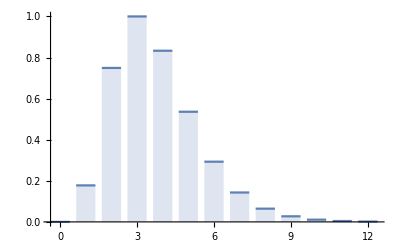

```mathematica
DiscretePlot[BiF[x/3,4],{x,0,12},ExtentSize->.75]
```

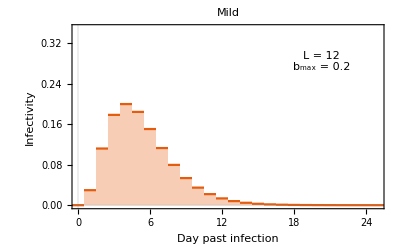
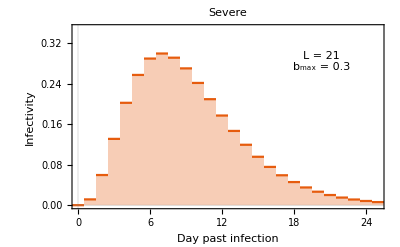
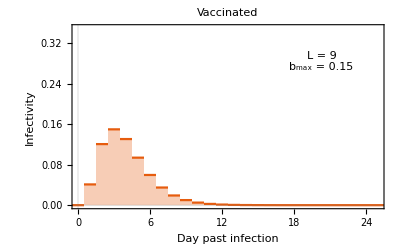

```mathematica
(*# infectivity profiles*)
MapThread[
DiscretePlot[Evaluate@(# BiF[(3x)/#2,#3]),{x,0,25},ExtentSize->Full,Frame->True,FrameLabel->{"Day past infection","Infectivity"},PlotTheme->"Scientific",PlotRange->{0,.35},PlotLabel->#4,
Epilog->Inset[Column[{"L = "<>ToString@#2,"b_max = "<>ToString@#},Alignment->Center,Spacings->0],Scaled@{.8,.8}],BaseStyle->12]&,
{{.2,.3,.15},{12,21,9},{3,3,3},{"Mild","Severe","Vaccinated"}}]
```

## College data

### Class schedule and dorm

```mathematica
(*Import complete class schedule*)
{StuB,CompCS}=<<"Class schedule 3000 4-22";
```

```mathematica
(*Campus residence*)
(SeedRandom["dorm"];
DormRes=
With[{n=Round[(*dorm fraction*).65 Length@StuB]},
Partition[RandomSample[StuB][[;;n]],(*Unit size*)UpTo@7]]);
```

```mathematica
(*Dorm mixing association*)
DormA=Merge[CompFun/@DormRes,Catenate];
```

## Run college

The model is implemented recursively on a daily basis. The model uses the previous day’s system state and the contact pools to calculate the probability of infection for susceptible hosts. The model determines who is infected and who is recovered, and updates the system state accordingly. All of the above iteration steps, illustrated above, are combined into a single code function. 
This function:

partitions the student pool into susceptible, infected, and recovered groups

calculates the probability of survival for susceptible individuals for different social activities: class mixing, dorm mixing, random social mixing

aggregates the probabilities of survival from the three environments into the overall probability of survival for a susceptible host

determines which susceptibles become infected

updates progress state of infected and determines which of them get recovered

creates the next daily system state reflecting any changes

### Basic community code

```mathematica
(*Baseline community code*)
CoM[(*system state*)ComState_,
(*Class risk assoc*)cRW_,
(*week day*)wd_,
(*dorm assoc*)dora_,
(*suceptibility assos*)susa_,
(*social mixing type*)RMT_,
(*mixing pattern*)miP_,
(*Environmental factors and class-distance scale*)
{aC_,aD_,aS_}]:=
Block[{Spo,spo,InfS,ClassMS,DorMS,rmP,mpA,DinMS,SPsurv,Sprob,SPInf},
(*S host status*)Spo=Select[ComState,#[[1]]==0&];
(*S hosts*)spo=Keys@Spo;
(*Infective status*)InfS=inF/@ComState;
(*class mixing survival*)
ClassMS=SurPC[cRW@wd,InfS,susa,spo,aC];
(*dorm mixing survival*)
DorMS=If[dora==<||>,<||>,SurMP[dora,InfS,susa,spo,aD]];
(*Random social mixing pools*)
rmP=RMT[Keys@ComState,miP];
(*Mix pool association*)
mpA=Merge[CompFun/@rmP,Catenate];
(*Survival probability for random mixing pools*)
DinMS=SurMP[mpA,InfS,susa,spo,aS];
(*Survival prob in all environments*)
SPsurv=Merge[{ClassMS,DorMS,DinMS},Times@@#&];
(*S->I probability*)Sprob=(RanBernDraw/@(1-SPsurv));
(*Combined S->I progress*) SPInf=Merge[{Spo,Sprob},(*S-progress function*)SProgF];
Join[(*Host progress*)ProG/@ComState,(*newly infected*)SPInf]]
```

#### Output code

We define a counting function for the number of students in each SIR disease state over time. Other important outputs include outbreak size (cumulative infection), peak, and duration.

The SIR counts however, give only crude account of community state and history, as host infectivities (disease stages) undergo large variations in the course of infection, which affect transmission dynamics and other possible outcome, e.g. diagnostic screening and quarantine isolation (see [4-5]). Here we assume symptomatic expression is associated with low infectivity, e.g. .01<b<.1. Values below are considered non-infective

We plot the SIR counting function over time.

```mathematica
(*SEIR counts code*)
SEI[Hi_]:=
With[{SEIR=CountsBy[Values@#,#[[1]]&]&/@Hi},
KeySort@Merge[KeyUnion[SEIR,0&],#&]]
(*Observed Outbreak duration, based on total-I*)
Dur[sei_]:=
With[{tz=sei@1},
If[Last@tz>0,Length@tz,FirstPosition[tz,0][[1]]]]
OutP[him_]:=
Block[{se=SEI@him,sh},
(*S history*)sh=se@0;
{(*Outbreak size*)sh[[1]]-sh[[-1]],(*duration*)Dur[se]}]
(*Infectivity data of community snapshot hi*)
InfP[hi_]:=
Block[
{(*Select infected*)gz=KeyDrop[GroupBy[Select[hi,#[[1]]==1&],#[[2]]&],(*drop day 0*)0],gip},
(*Infectivity*)gip=Map[inF,gz,{2}];Catenate[Values[Values/@gip]]]
(*Print outputs of community history*)
OPrin[him_]:=TableForm[{OutP@him},TableHeadings->{None,{"Size","Duration"}},TableAlignments->Center]
```

### Basic CoM

#### Initialize

```mathematica
(*Naive pool with {"M","S"} pathways ={.6,.4} no immune/ vaccination; inoculate 3*)
InM=
(SeedRandom["InM"];
With[{(*Naive pool*)
hn=NaiV[StuB,(*R*)0,(*V*)0,(*M*).6]},
InoC[hn,3]]);
```

```mathematica
(*SIR with {"M","S"} pathways w/o vaccination, 10% immune*)
InC=
(SeedRandom["InC"];
With[{(*Naive pool*)
hn=NaiV[StuB,(*R*).1,(*V*)0,(*M*).6]},
InoC[hn,4]]);
```

```mathematica
(*SIR with 2 pathways {"M","S"} and 50% vaccinated*)
InV=
(SeedRandom["InV"];
With[{(*Naive pool*)
hn=NaiV[StuB,(*R*)0,(*V*).9,(*M*).6]},
InoC[hn,4]]);
```

```mathematica
(*Social Mixing pattern*)
mixP={{6,4,2,1.},{2,3,4,5}};
(*high environmental risk factors*)
evRH={(*class*).25,(*dorm*).3,(*social*).2};
(*moderate environmental risk factors*)
evRM={(*class*).2,(*dorm*).25,(*social*).15};
(*low environmental risk factors*)
evRL={(*class*).15,(*dorm*).2,(*social*).1};
```

#### Test steps

```mathematica
(*Suceptibility association*)
SuSA=aH[Last@#]&/@InC;
(*Class risk association with d-scale=1.5*)
ClaRF=AssociationMap[ClaNR[CompCS,(*d-scale*)1.5,#]&,Week];
```

```mathematica
in2=
CoM[InC,(*Class risk*)ClaRF,
(*day*)"T",
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRM];
(*Count numbers in S-I-R*)
KeySort@CountsBy[Values@in2,#[[1]]&]
```

<|0→13496,1→4,2→1500|>

```mathematica
(*next*)
in2=
CoM[in2,(*Class risk*)ClaRF,
(*day*)"T",
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRM];
(*Count numbers in S-I-R*)
KeySort@CountsBy[Values@in2,#[[1]]&]
```

<|0→13496,1→4,2→1500|>

### Run history

```mathematica
(*Suceptibility association*)
SuSA=aH[Last@#]&/@InC;
(*Class risk association with d-scale=1.5*)
ClaRF=AssociationMap[ClaNR[CompCS,(*d-scale*)1.5,#]&,Week];
```

#### Naive history: moderate risk

```mathematica
(*15 week history*)
Hic=
FoldList[
CoM[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRL]&,
InV,
WeR@30];//AbsoluteTiming
```

{91.0113,Null}

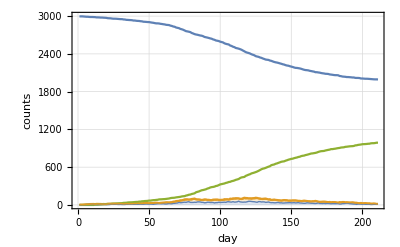

```mathematica
(*aggregate SIR*)
SE0=SEI@Hic;
sirP=ListLinePlot[Values@SE0,PlotStyle->{},PlotRange->{0,3000},Frame->True,PlotTheme->"Detailed",BaseStyle->12];
(*Infectivity profile history*)
ipH=InfP/@Hic;
(*Asymptomatic/symptomatic*)
ASin=Merge[KeyUnion[CountsBy[#,UnitStep[#-.05]&]&/@ipH]/.Missing[__]->0,#&];
Show[
sirP,StackedListPlot[{ASin@1,ASin@0},PlotStyle->{Thin}],FrameLabel->{"day","counts"}]
```

#### Naive history: moderate risk +reduced d-scale for class-risk

```mathematica
(*15 week history*)
Hid=
FoldList[
CoM[#,(*Class risk with low d*)ClaRd,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRM]&,
InC,
WeR@15];//AbsoluteTiming
```

{13.1195,Null}

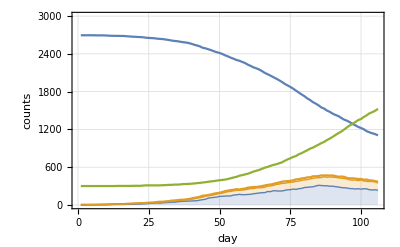

```mathematica
(*aggregate SIR*)
With[{Hi=Hid},
SE0=SEI@Hi;
sirP=ListLinePlot[Values@SE0,PlotStyle->{},PlotRange->{0,3000},Frame->True,PlotTheme->"Detailed",BaseStyle->12];
(*Infectivity profile history*)
ipH=InfP/@Hi;
(*Asymptomatic/symptomatic*)
ASin=Merge[KeyUnion[CountsBy[#,UnitStep[#-.05]&]&/@ipH]/.Missing[__]->0,#&];
Show[
sirP,StackedListPlot[{ASin@1,ASin@0},PlotStyle->{Thin}],FrameLabel->{"day","counts"}]]
```

Class -risk distance scale is an important factor:

#### Naive: high risk

```mathematica
(*15 week history*)
Hib=
FoldList[
CoM[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRH]&,
InC,
WeR@15];//AbsoluteTiming
```

{11.8196,Null}

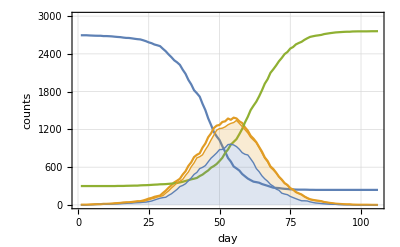

```mathematica
(*aggregate SIR*)
With[{Hi=Hib},
SE0=SEI@Hi;
sirP=ListLinePlot[Values@SE0,PlotStyle->{},PlotRange->{0,3000},Frame->True,PlotTheme->"Detailed",BaseStyle->12];
(*Infectivity profile history*)
ipH=InfP/@Hi;
(*Asymptomatic/symptomatic*)
ASin=Merge[KeyUnion[CountsBy[#,UnitStep[#-.05]&]&/@ipH]/.Missing[__]->0,#&];
Show[
sirP,StackedListPlot[{ASin@1,ASin@0},PlotStyle->{Thin}],FrameLabel->{"day","counts"}
(*,Epilog->Inset[OPrin[Hi],Scaled[{.5,.9}]]*)]]
```

#### Reduced class schedule

```mathematica
(*Reduced class schedule: 50% of each class*)
RedCS=(SeedRandom["RedCS"];{#[[1]],RandomSample[#[[2]],Round[.5Length@#[[2]]]]}&/@CompCS);
```

```mathematica
(*Class risk for reduced schedule with d-scale=1.5*)
ClaRm=AssociationMap[ClaNR[RedCS,(*d-scale*)1.5,#]&,Week];
```

```mathematica
(*15 week history*)
Hir=
FoldList[
CoM[#,(*reduced classes*)ClaRm,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRH]&,
InC,
WeR@15];//AbsoluteTiming
```

{27.2043,Null}

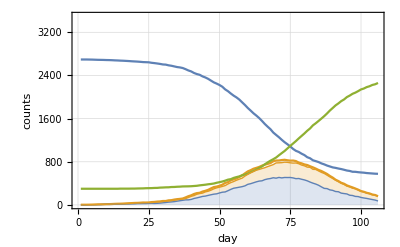

```mathematica
(*aggregate SIR*)
SE0=SEI@Hir;
sirP=ListLinePlot[Values@SE0,PlotStyle->{},PlotRange->{0,3500},Frame->True,PlotTheme->"Detailed",BaseStyle->12];
(*Infectivity profile history*)
ipH=InfP/@Hir;
(*Asymptomatic/symptomatic*)
ASin=Merge[KeyUnion[CountsBy[#,UnitStep[#-.05]&]&/@ipH]/.Missing[__]->0,#&];
Show[
sirP,StackedListPlot[{ASin@1,ASin@0},PlotStyle->{Thin}],FrameLabel->{"day","counts"}
(*,Epilog->Inset[OPrin[Hi],Scaled[{.5,.9}]]*)]
```

#### Ensemble

Model stochasticity, random social mixing and S->I progression, makes each history random. Here we compute an ensemble of such histories

```mathematica
(*Class risk*)
```

```mathematica
EHi=
Table[
FoldList[
CoM[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRL]&,
InV,
WeR@50],
{50}];
```

```mathematica
(*All ensemble histories*)SEir=SEI/@EHi;
SEa=Merge[SEir,#&];
```

```mathematica
(*Ensemble outputs*)
outE=OutP/@EHi
```

{{249,116},{1032,240},{802,258},{837,189},{1043,172},{851,267},{898,337},{670,228},{982,204},{33,48},{694,260},{11,26},{846,327},{1,14},{7,22},{44,52},{2,22},{1084,238},{5,21},{908,209},{900,223},{981,235},{608,247},{1027,234},{1018,244},{28,63},{21,55},{864,226},{3,30},{1090,225},{1043,344},{6,24},{809,221},{921,269},{1111,248},{1114,295},{871,274},{43,94},{896,282},{939,241},{863,182},{980,253},{36,70},{857,174},{1108,169},{487,179},{944,193},{921,199},{948,237},{10,33}}

```mathematica
{Mean@outE,StandardDeviation[outE]}//N
```

{{648.92,180.26},{425.501,97.5068}}

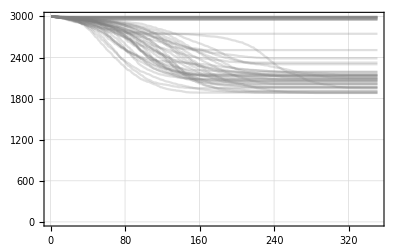
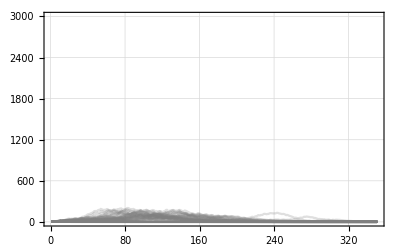
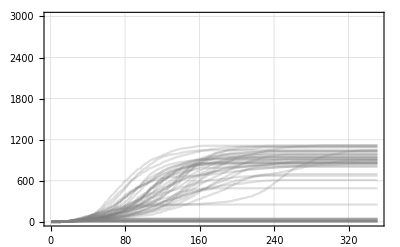
<|0→-Graphics-,1→-Graphics-,2→-Graphics-|>

```mathematica
ListLinePlot[#,Frame->True,PlotTheme->"Detailed",PlotStyle->{{Gray,Opacity@.25}},PlotRange->{0,3000}]&/@SEa
```

#### Run vaccinated history

```mathematica
(*Full class schedule*)
Hiv=
FoldList[
CoM[#,(*Class risk full schedule*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRH]&,
(*50% vaccine*)InV,
WeR@15];//AbsoluteTiming
```

{14.3831,Null}

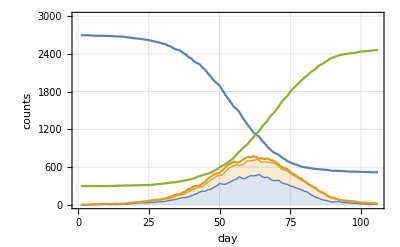

```mathematica
(*aggregate SIR*)
With[{Hi=Hiv},
SE0=SEI@Hi;
sirP=ListLinePlot[Values@SE0,PlotStyle->{},PlotRange->{0,3000},Frame->True,PlotTheme->"Detailed",BaseStyle->12];
(*Infectivity profile history*)
ipH=InfP/@Hi;
(*Asymptomatic/symptomatic*)
ASin=Merge[KeyUnion[CountsBy[#,UnitStep[#-.05]&]&/@ipH]/.Missing[__]->0,#&];
Show[
sirP,StackedListPlot[{ASin@1,ASin@0},PlotStyle->{Thin}],FrameLabel->{"day","counts"}]]
```

#### Run history ensemble

```mathematica
(*15 week ensemble*)
HiM=
ParallelTable[
(FoldList[
CoM[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRH]&,
InM,
WeR@15]),
{15}];//AbsoluteTiming
```

$Aborted

```mathematica
(*All ensemble histories*)SEir=SEI/@HiM;
SEa=Merge[SEir,#&];
```

```mathematica
(*Ensemble outputs*)
outE=OutP/@HiM;
```

```mathematica
{Mean@outE,StandardDeviation[outE]}//N
```

{{2913.06,91.625},{8.8353,6.18466}}

```mathematica
ListLinePlot[#,Frame->True,PlotTheme->"Detailed",PlotStyle->{{Gray,Opacity@.25}},PlotRange->{0,3000}]&/@SEa
```

```mathematica
(*Quantile envelop*)
SEq=Thread/@(Quantile[#,{.05,.5,.95}]&/@SEa);
```

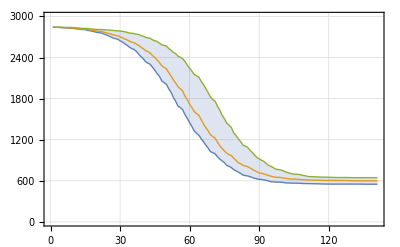
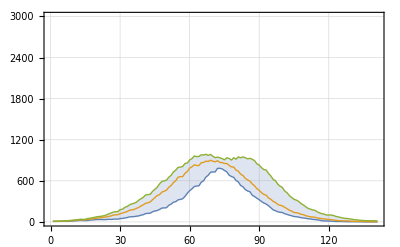
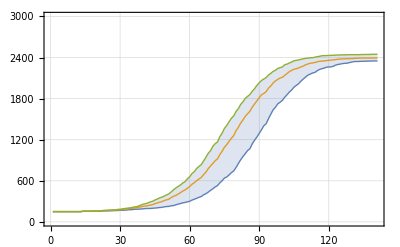
<|0→-Graphics-,1→-Graphics-,2→-Graphics-|>

```mathematica
ListLinePlot[#,PlotStyle->{Thin,Thick,Thin},Frame->True,PlotTheme->"Detailed",BaseStyle->14,Filling->{1->{3}},PlotRange->{0,3000}]&/@SEq
```

## Quarantine

Steps:
Symptomatic selection: applies to severe pathway,  P_sympt(d) -probability of symptoms
Test selection: applies to all pathways (S-M-V), P_test(inf) - probability of positive test = function of infectivity
QtW depends on recovery:  R_QP -> R_WP
3) Progress: S_WP get infected due to contacts; I_WP and I_QP undergo standard progress pathways

### Codes

```mathematica
(*Probability of Q selection*)
With[{pp=BiF[3d/L["S"],3]^{1,1/4}},
Plot[pp,{d,0,21},PlotLabels->{"Symptom", "test"},Frame->True,FrameLabel->{"Day","P-selection"},GridLines->Automatic]]
```

-Graphics-

#### Community code w. quarantine

```mathematica
(*Baseline community code*)
CoMQ[(*host pool*)HosP_,
(*Class risk assoc*)cRW_,
(*week day*)wd_,
(*dorm assoc*)dora_,
(*suceptibility assos*)susa_,
(*social mixing type*)RMT_,
(*mixing pattern*)miP_,
(*Environmental factors and class-distance scale*)
{aC_,aD_,aS_},
(*Q-selection function*)QSF_]:=Block[{nQ,wtq,WtQ,hpQ,Spo,spo,InfS,ClassMS,DorMS,rmP,mpA,DinMS,SPsurv,Sprob,SPInf},
(*Take non quarantine pool*)
nQ=Select[HosP,NumberQ@#[[1]]&];
(*Probability of Q selection*)
wtq=RanBernDraw[QSF@nQ];
(*Selected pool*)WtQ=Keys@Select[wtq,#==1&];(*Send to quarantine*)hpQ=Join[HosP,KeyTake[HosP,WtQ]/.{1,d_,p_}->{Q,d,p}];
(*S host status*)Spo=Select[hpQ,#[[1]]==0&];
(*S hosts*)spo=Keys@Spo;
(*Infective status*)InfS=inF/@hpQ;
(*class mixing survival*)
ClassMS=SurPC[cRW@wd,InfS,susa,spo,aC];
(*dorm mixing survival*)
DorMS=If[dora==<||>,<||>,SurMP[dora,InfS,susa,spo,aD]];
(*Random social mixing pools for nQ hosts*)
rmP=RMT[Keys@nQ,miP];
(*Mix pool association*)
mpA=Merge[CompFun/@rmP,Catenate];
(*Survival probability for random mixing pools*)
DinMS=SurMP[mpA,InfS,susa,spo,aS];
(*Survival prob in all environments*)
SPsurv=Merge[{ClassMS,DorMS,DinMS},Times@@#&];
(*S->I probability*)Sprob=(RanBernDraw/@(1-SPsurv));
(*Combined S->I progress*) SPInf=Merge[{Spo,Sprob},(*S-progress function*)SProgF];
Join[(*all host progress*)ProG/@hpQ,(*newly infected*)SPInf]]
```

### Run quarantine

#### Steps

```mathematica
(*day 40 previous history*)hp1=Hic[[40]];
```

```mathematica
in2=
CoMQ[hp1,(*Class risk*)ClaRF,
(*day*)"T",
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRH,
PSymp];
(*Count numbers in S-I-R*)
KeySort@CountsBy[Values@in2,#[[1]]&]
```

<|0→2291,1→271,2→377,Q→61|>

```mathematica
in2=
CoMQ[in2,(*Class risk*)ClaRF,
(*day*)"T",
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRM,
(*Q selection*)PSymp];
(*Count numbers in S-I-R*)
KeySort@CountsBy[Values@in2,#[[1]]&]
```

<|0→2266,1→269,2→379,Q→86|>

#### Run symptomatic Quarantine

```mathematica
(*Probability of symptomatic selection*)
PSymp[{1,d_,"S"}]=(*Max pobability of selection*).5BiF[3d/L["S"],3.];
PSymp[z_]=0;
(*Q-selection function for host pool hp*)
SymF[hp_]:=PSymp/@hp
```

```mathematica
(*15 week history*)
Hiq=
FoldList[
CoMQ[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRL,
(*symptomatic Q selection*)SymF]&,
InV,
WeR@40];//AbsoluteTiming
```

{138.938,Null}

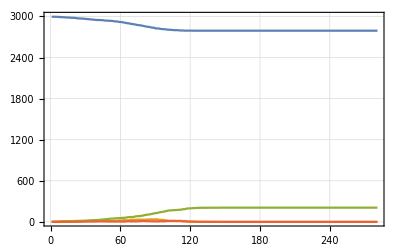

```mathematica
(*aggregate SIR*)
SEq=SEI@Hiq;
sirP=ListLinePlot[Values@SEq,PlotStyle->{},PlotRange->{0,3000},Frame->True,PlotTheme->"Detailed",BaseStyle->12]
```

#### Ensemble

```mathematica
(*Class risk*)
```

```mathematica
EHiq=
Table[
FoldList[
CoMQ[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRH,
(*symptomatic Q selection*)SymF]&,
InV,
WeR@20],
{50}];
```

```mathematica
(*All ensemble histories*)SEir=SEI/@EHiq;
SEa=Merge[SEir,#&];
```

```mathematica
(*Ensemble outputs*)
outE=OutP/@EHiq
```

{{1741,141},{1600,137},{1586,141},{1694,141},{1662,124},{1706,113},{1698,141},{1698,130},{1539,120},{1564,141},{1726,125},{1588,139},{1651,141},{1678,141},{1696,125},{1685,141},{1634,120},{1783,141},{1652,141},{1658,141},{1660,135},{1615,141},{1541,141},{1639,141},{1585,134},{1585,141},{1502,141},{1635,141},{1596,141},{1569,141},{1546,141},{1715,130},{1639,128},{1568,139},{1660,128},{1719,114},{1658,127},{1678,141},{1579,132},{1605,113},{1622,128},{1529,137},{1772,129},{1719,120},{1687,116},{1653,141},{1625,133},{1775,112},{1691,137},{1612,141}}

```mathematica
{Mean@outE,StandardDeviation[outE]}//N
```

{{1644.36,133.36},{66.77,9.41506}}

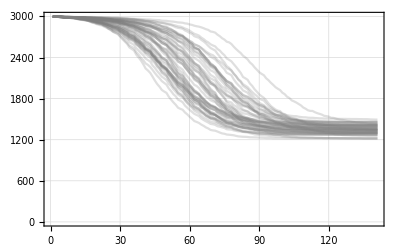
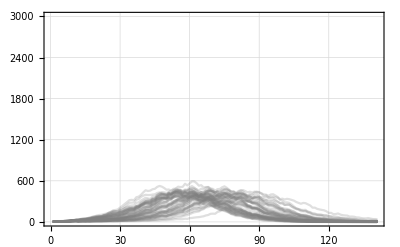
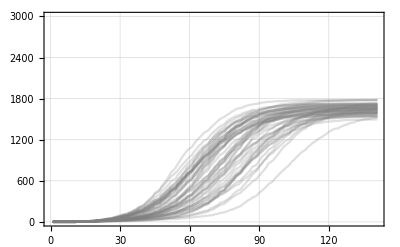
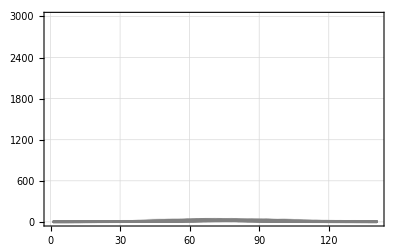
<|0→-Graphics-,1→-Graphics-,2→-Graphics-,Q→-Graphics-|>

```mathematica
ListLinePlot[#,Frame->True,PlotTheme->"Detailed",PlotStyle->{{Gray,Opacity@.25}},PlotRange->{0,3000}]&/@SEa
```

#### Mix history: 5 weeks baseline + 10 week symptomatic Q

```mathematica
(*baseline case*)
Hib=
FoldList[
CoM[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRM]&,
InC,
WeR@15];//AbsoluteTiming
```

{20.8279,Null}

```mathematica
(*Run symptomatic Q after week 5*)
Hiq=
FoldList[
CoMQ[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRL,
(*symptomatic Q selection*)SymF]&,
(*day 36*)Hib[[36]],
WeR@10];//AbsoluteTiming
```

{19.3832,Null}

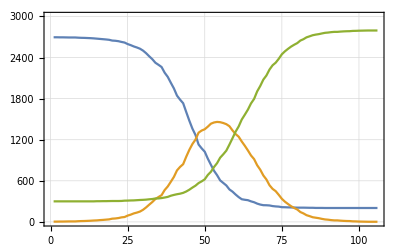

```mathematica
(*Baseline history*)
(*aggregate SIR*)
SEb=SEI@Hib;
ListLinePlot[Values@SEb,]
```

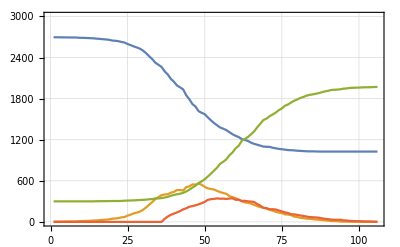

```mathematica
(*Combined Q history*)
Hiz=Join[Hib[[;;35]],Hiq];
(*aggregate SIR*)
SEz=SEI@Hiz;
ListLinePlot[Values@SEz,]
```

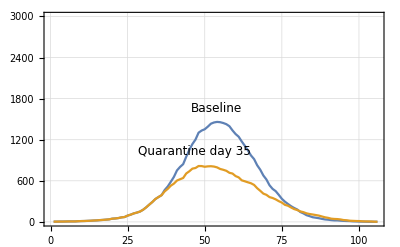

```mathematica
ListLinePlot[{SEb@1,SEz@1+SEz@Q},,PlotLabels->Placed[{"Baseline","Quarantine day 35"},Above]]
```

#### Community code w. quarantine and testing

```mathematica
(*Baseline community code*)
CoMS[(*host pool*)HosP_,
(*Class risk assoc*)cRW_,
(*week day*)wd_,
(*dorm assoc*)dora_,
(*suceptibility assos*)susa_,
(*social mixing type*)RMT_,
(*mixing pattern*)miP_,
(*Environmental factors and class-distance scale*)
{aC_,aD_,aS_},
(*Q-selection function*)QSF1_,
(*Q-selection function*)QSF2_]:=Block[{nQ,wtq,WtQ,hpQ1,hpQ,Spo,spo,InfS,ClassMS,DorMS,rmP,mpA,DinMS,SPsurv,Sprob,SPInf},
(*Take non quarantine pool*)
nQ=Select[HosP,NumberQ@#[[1]]&];
(*Probability of Q selection*)
wtq=RanBernDraw[QSF1@nQ];
(*Selected pool*)WtQ=Keys@Select[wtq,#==1&];(*Send to quarantine*)hpQ1=Join[HosP,KeyTake[HosP,WtQ]/.{1,d_,p_}->{Q,d,p}];
nQ=Select[hpQ1,NumberQ@#[[1]]&];
(*Probability of Q selection*)
wtq=RanBernDraw[QSF2@nQ];
(*Selected pool*)WtQ=Keys@Select[wtq,#==1&];(*Send to quarantine*)hpQ=Join[hpQ1,KeyTake[hpQ1,WtQ]/.{1,d_,p_}->{Q,d,p}];
(*S host status*)Spo=Select[hpQ,#[[1]]==0&];
(*S hosts*)spo=Keys@Spo;
(*Infective status*)InfS=inF/@hpQ;
(*class mixing survival*)
ClassMS=SurPC[cRW@wd,InfS,susa,spo,aC];
(*dorm mixing survival*)
DorMS=If[dora==<||>,<||>,SurMP[dora,InfS,susa,spo,aD]];
(*Random social mixing pools for nQ hosts*)
rmP=RMT[Keys@nQ,miP];
(*Mix pool association*)
mpA=Merge[CompFun/@rmP,Catenate];
(*Survival probability for random mixing pools*)
DinMS=SurMP[mpA,InfS,susa,spo,aS];
(*Survival prob in all environments*)
SPsurv=Merge[{ClassMS,DorMS,DinMS},Times@@#&];
(*S->I probability*)Sprob=(RanBernDraw/@(1-SPsurv));
(*Combined S->I progress*) SPInf=Merge[{Spo,Sprob},(*S-progress function*)SProgF];
Join[(*all host progress*)ProG/@hpQ,(*newly infected*)SPInf]]
```

### Test screening

Random draw of 150 non-quarantine students for daily test

```mathematica
(*Test selection*)
PTest[{1,d_,pw_}]=BiF[3d/L[pw],3.]^(1/4);
PTest[z_]=0;
(*Test screening function for m daily tests *)
TSF[m_]:=PTest/@RandomSample[#,m]&
```

#### Random tests after day 35

```mathematica
(*Run testing after week 5 with 150 randomly drawn tests/day*)
Hit=
FoldList[
CoMS[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRM,
(*symptomatic Q selection*)SymF,TSF[150]]&,
InV,
WeR@50];//AbsoluteTiming
```

{151.667,Null}

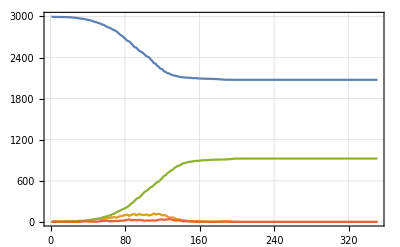

```mathematica
(*Combined Q history*)
Hig=Join[Hib[[;;5]],Hit];
(*aggregate SIR*)
SEg=SEI@Hit;
ListLinePlot[Values@SEg,PlotStyle->{},PlotRange->{0,3000},Frame->True,PlotTheme->"Detailed",BaseStyle->12]
```

```mathematica
ListLinePlot[{SEb@1,SEg@1+SEg@Q},,PlotLabels->Placed[{"Baseline","Testing day 35"},Above]]
```

ListLinePlot::lpn: {{},{{1.,4.},{2.,4.},{3.,6.},{4.,7.},{5.,7.},{6.,7.},{7.,7.},{8.,7.},{9.,8.},{10.,8.},«341»}} is not a list of numbers or pairs of numbers.

ListLinePlot[{SEb[1],{4,4,6,7,7,7,7,7,8,8,8,4,5,3,2,2,2,3,5,4,4,5,8,7,7,9,12,13,12,15,16,17,20,17,17,19,23,24,25,27,27,28,32,32,35,40,42,41,40,42,49,47,49,50,55,55,53,56,63,69,69,69,70,72,78,73,77,79,81,78,76,81,87,95,103,101,105,107,122,121,132,136,135,126,126,126,130,135,145,137,136,120,128,133,145,140,136,127,120,122,118,125,129,123,118,110,121,122,130,141,142,136,127,140,141,146,151,148,138,132,129,129,126,130,119,113,108,102,97,99,99,88,76,73,66,61,60,58,55,48,41,36,33,32,29,27,22,20,19,18,17,19,15,12,12,10,10,11,12,12,11,11,7,8,8,8,9,8,7,5,5,5,5,5,4,3,5,5,6,7,8,7,7,9,11,11,13,11,11,10,9,7,8,8,5,3,3,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},PlotStyle→{},PlotRange→{0,3000},Frame→True,PlotTheme→Detailed,BaseStyle→12,PlotLabels→Placed[{Baseline,Testing day 35},Above]]

#### Ensemble

```mathematica
(*Class risk*)
```

```mathematica
EHit=
Table[
FoldList[
CoMS[#,(*Class risk*)ClaRF,
(*day*)#2,
(*housing*)DormA,
(*Susc*)SuSA,
(*random disjunct*)RanMixN,mixP,(*Moderate environmental risk*)evRM,
(*symptomatic Q selection*)SymF,TSF[150]]&,
InV,
WeR@5],
{50}];
```

```mathematica
(*All ensemble histories*)SEir=SEI/@EHit;
SEa=Merge[SEir,#&];
```

```mathematica
(*Ensemble outputs*)
outE=OutP/@EHit
```

{{78,36},{59,36},{93,36},{139,36},{14,36},{56,36},{80,36},{60,36},{4,23},{73,36},{58,36},{99,36},{100,36},{55,36},{151,36},{98,36},{80,36},{89,36},{104,36},{50,36},{137,36},{21,36},{145,36},{114,36},{103,36},{97,36},{211,36},{93,36},{30,36},{87,36},{31,36},{109,36},{68,36},{39,36},{118,36},{41,36},{87,36},{148,36},{69,36},{50,36},{25,36},{45,36},{119,36},{101,36},{59,36},{210,36},{209,36},{129,36},{147,36},{53,36}}

```mathematica
{Mean@outE,StandardDeviation[outE]}//N
```

{{88.7,35.74},{48.3623,1.83848}}

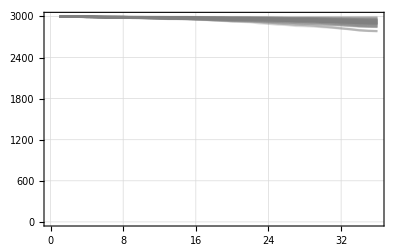
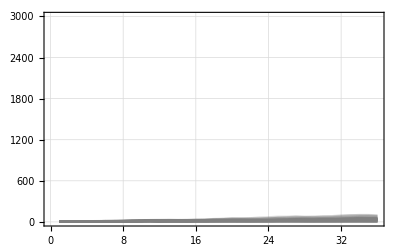
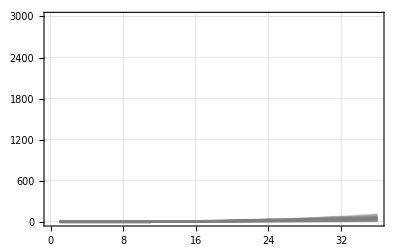
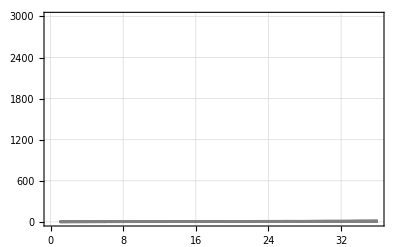
<|0→-Graphics-,1→-Graphics-,2→-Graphics-,Q→-Graphics-|>

```mathematica
ListLinePlot[#,Frame->True,PlotTheme->"Detailed",PlotStyle->{{Gray,Opacity@.25}},PlotRange->{0,3000}]&/@SEa
```